```mathematica
Universitatea Tehnică a Moldovei
Facultatea Calculatoare,Informatică și Microelectronică
Specialitatea Tehnologii Informaționale



-Graphics-

Raport
la lucrarea de laborator nr.4
Tema:“Reprezentarea datelor statistice”


Disciplina:“Probabilitate si statistica aplicata”
Varianta 3


A efectuat:                              Student TI-231 FR                                             Apareci Aurica
A verificat:                         Asistent universitar            Andrievschi-Bagrin Veronica




Chișinău 2024
```

```mathematica
Pentru datele extrase să se realizeze următoarele operații:1. Să se calculeze pentru fiecare regiune în parte
a.valoarea medie a nașterilor
b.dispersia
2. Să se calculeze pentru fiecare an în parte:
a.valoarea medie a nașterilor
b.dispersia
3. Să se reprezinte histogramele
4. Să se construiască poligonul frecvențelor
```

```mathematica
1. Calculul valorii medii și al dispersiei pentru fiecare regiune
```

```mathematica
a.Valoarea medie a nașterilor
```

```mathematica
Pentru Hîncești:
```

```mathematica
Mean[{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227}]
```

20693/15

```mathematica
Pentru Căușeni:
```

```mathematica
Mean[{1172,1059,1053,1065,1073,1083,1088,1044,952,1005,997,1003,1017,927,856}]
```

15394/15

```mathematica
Pentru Ocnița:
```

```mathematica
Mean[{500,477,445,488,538,529,507,477,509,466,436,464,431,428,395}]
```

1418/3

```mathematica
b.Dispersia nașterilor
```

```mathematica
Pentru Hîncești:
```

```mathematica
Variance[{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227}]
```

749008/105

```mathematica
Pentru Căușeni:
```

```mathematica
Variance[{1172,1059,1053,1065,1073,1083,1088,1044,952,1005,997,1003,1017,927,856}]
```

602617/105

```mathematica
Pentru Ocnița:
```

```mathematica
Variance[{500,477,445,488,538,529,507,477,509,466,436,464,431,428,395}]
```

34430/21

```mathematica
2. Calculul valorii medii și al dispersiei pentru fiecare an
```

```mathematica
a.Valoarea medie a nașterilor pentru 2004
```

```mathematica
Mean[{1554,1172,500}]
```

3226/3

```mathematica
b.Dispersia nașterilor pentru 2004
```

```mathematica
Variance[{1554,1172,500}]
```

854212/3

```mathematica
3. Reprezentarea histogramelor
```

```mathematica
Histogramă pentru Hîncești:
```

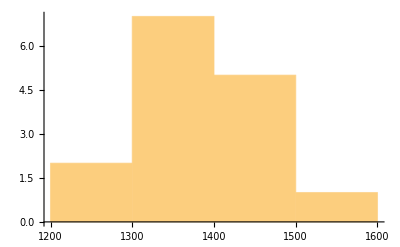

```mathematica
Histogram[{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227}]
```

```mathematica
Histogramă pentru Causeni:
```

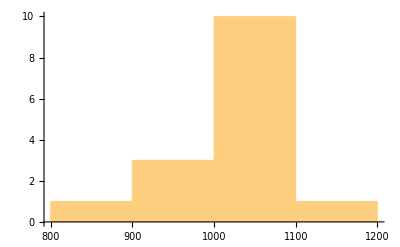

```mathematica
Histogram[{1172,1059,1053, 1065, 1073, 1083, 1088, 1044, 952, 1005, 997, 1003, 1017, 927,856}]
```

```mathematica
Histogramă pentru Ocnita:
```

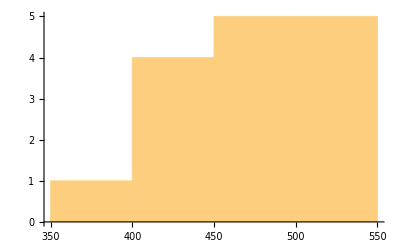

```mathematica
Histogram[{500,477,445, 488, 538, 529, 507, 477, 509, 466, 436, 464, 431, 428,395}]
```

```mathematica
Histogramă pentru toate raioanele:
```

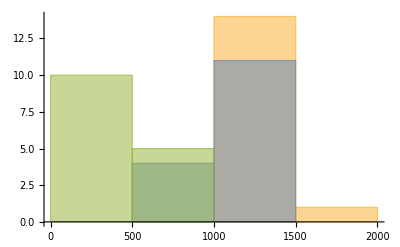

```mathematica
Histogram[{{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227},{1172,1059,1053, 1065, 1073, 1083, 1088, 1044, 952, 1005, 997, 1003, 1017, 927,856},{500,477,445, 488, 538, 529, 507, 477, 509, 466, 436, 464, 431, 428,395}}]
```

```mathematica
4. Construirea poligonului frecvențelor
```

```mathematica
Pentru Hîncești:
```

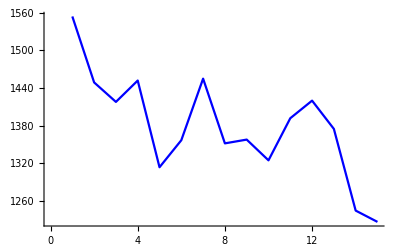

```mathematica
ListLinePlot[{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227},PlotStyle->Blue]
```

```mathematica
Pentru Causeni:
```

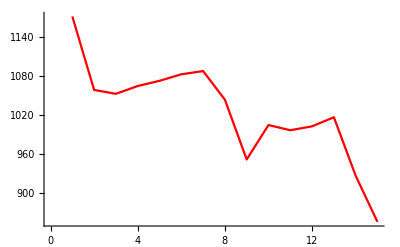

```mathematica
ListLinePlot[{1172,1059,1053, 1065, 1073, 1083, 1088, 1044, 952, 1005, 997, 1003, 1017, 927,856},PlotStyle->Red]
```

```mathematica
Pentru Ocnita:
```

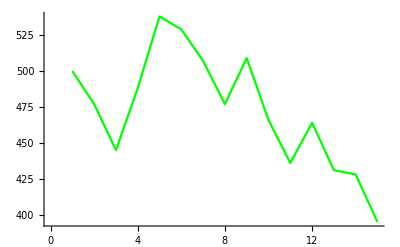

```mathematica
ListLinePlot[{500,477,445, 488, 538, 529, 507, 477, 509, 466, 436, 464, 431, 428,395},PlotStyle->Green]
```

```mathematica
Pentru toate raioanele pe același grafic (separate pentru fiecare raion):
```

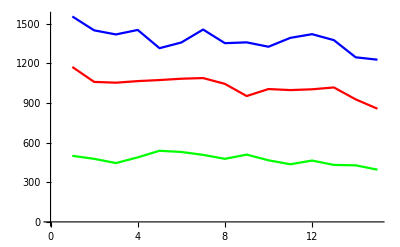

```mathematica
ListLinePlot[{{1554,1449,1418,1452,1314,1357,1455,1352,1358,1325,1392,1420,1375,1245,1227},{1172,1059,1053, 1065, 1073, 1083, 1088, 1044, 952, 1005, 997, 1003, 1017, 927,856},{500,477,445, 488, 538, 529, 507, 477, 509, 466, 436, 464, 431, 428,395}},PlotStyle->{Blue,Red,Green}]
```

```mathematica
Sarcina 2
Având la dispoziție rezultatele din exercițiul 7 lucrarea de laborator nr.3,să se introducă datele într-un tabel (ex.Tabelul1,suportul teoretic) și să se obțină următoarele rezultate:a) histograma
b) poligonul frecvențelor Înălţimea unui bărbat este o v.a.cu repartiţia normală.Presupunem că această repartiţie are parametrii
m=175+(-1)n /n cm şi =6-(-1)n /n cm.Să se formeze programul de conficţionate a costumelor bărbăteşti pentru o fabrică de confecţii care se referă la asigurarea cu costume a bărbaţilor,înălţimile cărora aparţin intervalelor:[150,155),[155,160),[160,165),[165,170),[170,175),[175,180),[180,185),[185,190),[190,195),[195,200],n fiind numarul variantei,n=1,2,…30.
```

RandomVariate::posprm: Parameter σ at position 2 in NormalDistribution[m,σ] is expected to be positive.

Histogram::hbins: The bin specification {150,155,160,165,170,175,180,185,190,195,200} cannot be used to determine either how many or which bins to use.

```mathematica
m=175+(-1)^1/1
σ=6-(-1)^1/1
```

174

7

```mathematica
Histogram[RandomVariate[NormalDistribution[m,σ],1000],{150,155,160,165,170,175,180,185,190,195,200}]
```

Histogram::hbins: The bin specification {150,155,160,165,170,175,180,185,190,195,200} cannot be used to determine either how many or which bins to use.

Histogram[{176.575,174.99,173.129,168.105,170.033,166.24,181.61,177.621,177.714,171.644,172.727,165.572,183.407,172.638,175.237,174.196,169.085,179.197,161.114,176.161,170.538,184.082,169.608,174.292,184.058,170.191,174.553,175.956,180.404,167.424,177.028,176.587,174.739,178.257,182.04,187.903,175.391,173.257,178.437,172.173,161.946,177.166,183.424,168.029,160.705,177.169,172.624,175.939,178.55,181.084,176.96,170.782,167.741,166.557,173.685,182.769,170.379,193.387,162.337,163.857,175.962,172.323,174.214,175.204,185.261,163.631,163.92,182.869,181.272,176.835,175.738,178.481,184.119,168.049,171.087,183.512,173.137,190.639,181.408,170.405,169.626,178.281,176.259,176.038,160.736,161.352,173.44,176.328,170.708,152.663,175.823,177.178,171.657,175.042,184.523,171.018,186.635,165.271,180.62,170.558,179.982,165.946,173.698,172.384,177.415,177.796,182.372,170.143,175.479,184.384,162.611,178.7,164.86,172.942,175.089,177.426,184.193,177.123,170.155,172.354,179.401,171.088,189.948,170.096,170.134,176.986,169.217,185.12,180.803,173.615,161.413,169.969,168.023,183.982,189.836,172.473,191.691,176.865,167.104,173.411,181.469,171.723,174.872,167.284,177.957,170.501,182.284,194.022,163.524,175.286,188.302,170.285,180.008,167.463,181.511,157.355,172.235,180.759,166.605,158.089,185.873,175.251,172.917,169.058,180.804,179.506,176.474,167.221,179.442,171.163,174.103,149.347,175.671,171.613,187.943,184.137,176.835,169.894,174.828,176.707,162.653,174.955,183.889,172.615,186.272,175.407,185.157,172.581,169.719,179.073,185.748,169.911,171.455,172.823,179.216,173.201,177.661,173.619,166.2,171.634,184.937,174.677,165.989,171.372,170.715,177.739,164.702,175.963,178.995,180.475,171.814,168.378,174.091,174.611,162.573,169.501,180.644,189.386,177.516,168.663,160.891,178.377,168.198,176.744,168.101,184.872,164.568,178.97,174.26,169.643,190.842,167.082,176.061,171.396,176.416,176.836,167.197,168.181,176.37,178.802,181.317,179.137,167.822,171.314,166.05,175.142,171.461,178.445,172.801,168.346,179.113,181.954,163.154,172.925,162.613,169.078,168.705,170.301,187.147,179.764,176.626,185.087,182.348,188.107,172.182,175.941,167.968,181.465,172.973,184.086,181.096,179.01,170.385,178.001,167.277,173.935,175.855,172.125,182.281,181.57,167.579,158.505,178.549,178.768,176.739,172.623,169.589,182.492,172.337,174.709,170.126,172.521,173.116,175.209,176.971,180.919,176.064,175.133,173.453,162.672,181.973,172.368,184.296,176.203,174.204,182.005,168.244,177.664,171.879,168.702,172.663,177.867,175.435,174.329,182.542,180.323,168.837,173.618,178.657,164.385,175.027,176.755,159.471,187.691,177.957,174.202,165.647,176.001,178.48,168.475,189.075,170.87,169.888,169.547,168.379,175.425,169.978,170.977,168.827,177.543,181.732,178.412,166.712,178.014,172.004,167.112,169.615,175.378,168.692,154.901,178.713,168.908,165.269,170.841,174.501,181.518,158.952,181.088,176.189,185.661,170.084,179.608,172.015,185.171,173.011,167.55,176.646,171.532,168.188,178.345,161.295,170.082,185.264,178.578,174.586,170.41,170.429,166.504,175.703,179.174,161.674,172.319,169.069,164.191,168.819,183.015,167.996,166.621,163.762,172.411,179.606,168.47,170.056,171.311,171.582,178.072,176.093,177.674,179.033,172.667,157.079,174.322,165.185,166.949,166.686,173.646,179.372,179.424,170.223,172.758,165.394,187.543,158.672,166.972,183.191,171.718,177.587,176.254,173.832,173.429,173.6,162.529,166.94,183.455,184.29,171.828,174.201,163.555,175.182,172.151,172.086,176.509,193.606,175.793,167.433,176.462,179.816,181.107,175.252,167.024,184.022,176.843,180.361,164.464,181.005,170.24,173.48,171.88,168.146,173.81,174.314,158.993,162.382,177.103,177.094,169.681,179.37,179.668,181.393,163.212,171.938,167.442,167.064,177.465,170.884,170.291,188.273,184.371,179.441,172.693,170.301,165.889,180.13,166.815,179.776,168.489,173.55,164.862,169.906,173.008,160.562,168.753,179.231,172.706,178.027,165.574,165.348,159.87,166.224,166.329,177.624,180.168,178.611,183.182,177.627,159.516,178.309,173.592,178.508,178.632,179.241,189.039,179.077,176.761,177.494,177.418,165.09,180.665,190.531,172.955,180.283,174.976,177.258,178.576,172.722,178.654,185.211,173.934,165.325,183.07,166.62,162.364,165.53,164.517,185.303,176.31,162.394,165.508,175.759,170.166,175.725,180.721,174.323,181.375,168.063,177.257,182.898,183.326,177.829,162.688,173.057,168.237,165.378,179.021,176.312,164.583,174.162,186.024,169.841,182.09,170.111,177.232,170.537,173.005,170.624,178.707,170.58,178.638,163.407,180.72,174.534,178.546,171.67,172.712,181.155,164.992,177.374,170.708,173.87,161.369,169.963,160.149,165.476,181.447,170.988,179.543,162.716,174.905,173.822,182.746,181.194,172.81,172.695,178.609,178.158,172.909,189.856,173.132,180.574,168.917,172.094,176.652,179.733,179.548,184.408,164.337,171.697,177.891,172.732,171.934,187.623,172.475,179.798,172.957,175.177,167.013,170.139,169.124,180.586,171.981,173.824,168.912,176.558,172.697,176.939,179.672,173.491,178.516,178.294,173.583,166.69,170.501,170.664,188.39,175.826,172.353,180.191,163.465,168.753,163.541,178.083,165.043,176.632,182.004,181.389,179.872,165.888,165.12,181.178,174.836,175.35,172.732,175.324,181.115,178.818,168.042,171.747,181.331,175.849,180.519,176.34,176.732,175.51,176.687,173.688,172.243,156.674,177.075,170.254,169.944,171.804,161.324,167.48,176.571,169.704,168.47,164.988,172.821,168.519,180.171,162.558,165.865,178.526,171.394,191.369,177.781,177.756,169.691,170.029,179.805,170.667,173.98,174.502,178.088,185.705,166.503,178.015,180.759,162.644,177.438,184.92,171.638,177.398,176.511,183.822,176.444,166.723,167.287,164.542,160.536,174.996,166.096,158.956,185.858,174.105,165.038,167.937,177.806,173.757,159.796,187.68,185.915,178.282,174.053,164.208,170.041,174.156,175.168,167.328,174.128,178.769,168.776,175.542,166.759,169.865,179.02,173.049,174.823,181.715,173.342,171.783,165.928,169.689,182.598,173.776,153.408,172.465,186.543,186.446,172.681,170.024,170.142,164.548,180.277,181.653,171.099,183.285,154.324,171.244,180.728,174.032,172.937,181.692,177.973,173.038,166.997,176.013,175.224,179.828,177.905,161.115,175.123,162.236,169.491,171.896,168.267,171.02,175.005,177.337,171.786,175.832,158.641,173.003,172.243,184.212,184.218,167.407,181.537,173.689,179.872,172.925,187.051,169.048,168.901,178.083,166.54,164.859,173.111,163.157,171.427,176.491,177.033,168.91,189.466,175.978,172.52,169.749,182.032,171.691,167.822,167.97,163.673,178.938,174.407,176.271,182.016,190.237,174.914,166.134,183.869,179.234,175.147,175.26,173.134,171.254,172.748,177.597,164.837,172.83,189.843,174.997,174.958,180.917,177.206,180.037,171.588,165.179,180.765,174.07,171.075,179.817,177.979,164.702,178.541,178.985,171.006,170.741,170.208,167.207,173.81,180.091,162.488,177.069,162.412,175.948,167.547,182.319,177.024,175.876,169.508,172.394,174.383,165.048,178.919,180.775,169.974,173.484,172.547,169.064,161.195,183.646,176.972,180.464,178.78,180.049,162.403,170.84,176.745,171.774,160.414,170.931,182.311,173.081,172.039,164.996,166.103,184.893,170.887,165.336,163.893,161.348,178.237,174.498,185.454,177.25,176.521,165.291,182.404,172.999,174.029,181.317,173.723,166.798,180.616,163.839,169.765,180.191,177.577,171.777,185.974,169.618,170.421,175.908,166.02,181.224,178.714,178.964,185.665,168.884,171.5,177.595,185.242,178.745,180.055,172.657,185.427,170.017,170.708,186.065,174.591,173.491,160.572,180.248,180.935,160.189,171.092,161.668,175.159,163.63,177.355,174.56,174.888,168.841,176.389,181.058,178.131,171.24,173.478,162.859,180.396,184.873,180.67,188.214,172.874,179.91,185.78,163.044,155.639,174.941,173.836,171.493,168.814,177.636,182.151,172.506,181.978,169.934,174.098,184.355,174.412,173.108,181.879,157.128,191.609,170.894,174.916,176.299,170.611,172.982,170.061,175.089,180.12,182.63,174.012,178.036,167.227,177.573,184.987,170.442,181.051,184.319,177.371,183.86,180.028,176.458,180.74,178.606,172.103,161.84,170.82,167.542,173.038,174.44,167.871,175.796,182.541,177.763,184.876,169.714,188.309},{150,155,160,165,170,175,180,185,190,195,200}]

```mathematica
frequencies=BinCounts[RandomVariate[NormalDistribution[m,σ],1000],{150,155,160,165,170,175,180,185,190,195,200}]
-Graphics-
```

BinCounts::bins: The bin specification {150,155,160,165,170,175,180,185,190,195,200} is not a list of 2 or 3 real values.

BinCounts[{162.986,173.23,168.269,171.148,186.738,163.57,183.043,166.867,166.314,180.726,169.343,172.863,169.198,158.471,191.722,188.556,177.971,169.666,176.125,176.486,165.922,175.049,178.293,174.39,180.697,174.004,181.39,183.133,180.479,170.144,184.769,162.513,178.951,178.918,185.564,175.932,171.197,170.586,179.318,172.761,186.577,173.868,168.562,167.705,179.543,187.416,166.513,171.349,177.057,172.161,179.495,178.092,178.45,182.38,168.885,168.288,166.301,176.439,167.252,171.816,175.598,168.299,173.638,173.339,172.895,171.202,169.122,173.979,177.983,180.729,175.254,176.347,176.731,171.83,173.514,157.948,175.921,183.322,177.516,168.935,170.67,180.008,172.298,176.402,175.75,164.367,175.274,177.614,169.405,175.006,168.181,183.81,179.171,176.27,163.662,175.709,168.173,172.707,162.742,173.844,175.854,170.649,167.624,174.012,176.744,174.835,161.282,162.607,184.172,176.997,174.883,186.077,187.635,172.549,170.223,162.087,180.896,181.82,164.744,170.002,171.609,177.767,177.171,177.913,181.747,175.757,176.919,191.361,163.086,172.776,177.721,172.559,186.387,161.457,171.241,184.42,177.911,177.211,172.488,174.81,176.19,171.923,175.758,174.988,173.913,172.146,175.538,174.987,181.909,168.921,172.193,171.234,167.674,180.821,160.918,190.732,175.408,171.302,173.336,185.903,175.082,170.005,190.165,185.224,182.031,172.683,174.008,170.109,171.331,179.689,159.997,174.212,168.921,178.527,166.795,172.08,171.996,179.45,174.394,177.594,179.651,169.645,171.876,167.392,178.1,158.906,172.124,174.885,178.292,162.776,172.819,182.435,162.42,174.544,164.06,177.887,172.63,181.104,173.072,175.209,180.407,175.758,188.397,180.801,173.198,184.986,180.505,170.301,183.453,182.42,181.011,166.993,170.196,197.153,170.507,171.562,183.012,180.582,165.169,168.121,173.043,186.306,168.15,168.2,175.315,171.877,173.923,167.596,162.417,176.713,174.392,168.859,181.944,185.825,178.18,170.953,174.712,188.842,163.048,168.576,162.446,171.553,173.666,171.462,159.381,179.629,162.671,178.757,177.183,170.797,173.93,176.391,178.128,173.232,174.867,180.084,184.944,167.031,175.937,173.205,165.347,176.653,176.544,163.064,184.637,175.515,166.257,166.222,169.859,177.102,171.114,165.509,177.161,170.006,170.975,171.856,178.208,169.087,181.72,173.157,187.613,169.812,182.432,180.518,170.251,177.76,169.786,180.062,182.614,167.73,178.455,174.508,178.53,166.792,169.947,169.533,160.07,164.818,173.666,167.268,168.217,166.845,173.331,175.263,164.952,166.307,176.808,165.516,176.954,179.545,178.348,154.838,177.717,180.407,178.208,173.575,185.834,173.283,171.748,182.37,158.328,164.715,183.048,180.261,177.167,173.811,177.305,158.994,180.893,179.492,171.351,169.857,167.486,173.157,172.002,177.671,172.208,173.239,167.409,176.748,178.125,172.35,173.961,169.188,175.889,170.8,177.889,173.292,181.53,159.631,175.327,181.304,160.467,173.305,180.889,181.07,179.635,176.106,179.645,162.391,172.19,174.554,181.675,170.767,168.97,169.278,164.264,166.346,167.1,175.467,182.15,180.254,173.225,173.518,176.241,169.86,178.624,174.65,175.585,168.344,175.823,176.228,163.459,170.792,172.811,174.139,195.1,180.976,161.937,179.322,179.918,179.176,166.199,170.574,179.832,165.265,174.053,161.339,180.609,185.972,183.558,170.266,178.22,180.742,177.428,183.337,170.221,181.056,173.851,174.155,180.887,180.02,171.809,174.301,171.908,166.642,174.069,170.118,182.681,172.452,185.201,169.806,175.652,159.779,177.68,175.489,180.916,172.473,160.209,169.812,183.123,169.822,170.565,158.68,173.288,182.656,164.554,180.855,174.075,175.522,173.253,180.877,170.719,166.203,169.958,171.488,172.364,169.106,168.545,174.895,173.422,169.086,176.345,184.062,161.09,170.256,163.035,173.947,169.826,182.247,182.177,182.832,179.959,165.485,186.56,175.913,177.314,175.005,179.875,178.601,170.136,166.089,174.023,164.744,174.917,181.031,179.51,175.026,183.207,169.876,178.175,168.964,184.186,176.693,173.028,167.608,168.88,167.926,178.999,162.707,171.461,178.382,184.232,192.82,166.211,177.207,163.166,163.762,157.988,180.246,177.402,168.807,170.939,158.764,174.281,170.17,162.792,182.427,181.837,174.091,186.312,174.914,177.348,176.499,179.338,180.359,174.442,180.022,172.103,173.21,175.983,174.435,161.442,177.353,173.451,172.332,185.056,177.344,170.051,164.655,172.405,176.117,162.803,185.861,168.4,181.359,166.384,175.709,186.757,171.701,166.525,162.223,172.849,181.446,163.146,177.184,183.092,157.417,164.937,189.225,165.973,174.453,176.337,166.046,162.867,178.437,181.136,173.411,171.85,180.144,177.4,168.498,165.179,175.004,163.32,167.145,176.198,181.976,175.912,173.449,171.97,185.793,165.604,167.264,166.023,176.186,179.347,179.569,167.547,182.802,169.581,167.589,178.005,174.783,165.52,174.806,169.407,173.124,181.442,165.544,177.787,173.318,160.569,165.852,161.835,170.926,158.958,168.965,174.783,178.446,163.176,171.913,170.885,170.834,182.94,186.819,173.943,180.281,166.258,172.759,172.338,173.803,163.931,179.436,182.121,180.426,162.779,177.439,163.008,183.157,181.599,181.193,171.306,178.415,173.484,172.316,176.411,170.197,167.373,168.981,169.431,180.17,176.052,164.982,171.99,181.407,174.796,180.754,175.277,168.541,185.306,170.753,173.584,168.315,165.951,178.932,170.331,165.254,174.488,184.212,166.783,160.598,167.64,171.92,177.119,177.422,167.513,177.646,177.41,170.355,181.581,161.628,173.036,176.747,181.615,160.424,171.319,158.942,167.104,179.301,183.111,177.994,165.543,177.383,172.07,165.781,180.858,170.26,172.913,172.603,175.676,180.421,166.958,172.213,190.741,182.34,180.041,176.084,171.323,179.454,169.944,176.54,177.678,181.292,172.479,189.84,162.673,170.493,168.762,172.513,179.713,172.277,172.718,185.741,160.329,164.946,165.672,173.015,175.536,161.917,175.407,167.864,180.087,169.065,177.49,184.45,171.539,163.944,170.402,173.448,176.625,186.113,163.152,165.337,161.897,159.925,172.716,176.512,180.039,169.105,170.65,182.222,188.488,175.056,166.074,178.01,166.877,177.819,164.056,171.728,173.694,175.575,170.6,179.417,186.827,172.339,184.227,191.185,175.58,178.304,168.721,186.821,175.683,162.366,166.738,173.416,183.926,160.647,166.039,176.156,176.588,173.338,162.018,186.937,174.042,168.893,156.64,168.819,189.232,167.29,164.242,164.458,174.784,181.643,180.781,176.027,179.81,177.014,180.431,159.523,174.348,180.912,164.866,180.992,165.019,178.286,172.536,162.498,181.143,179.46,166.036,177.987,184.96,164.727,172.655,172.576,168.216,178.655,182.038,162.744,171.469,175.358,174.557,166.97,184.205,174.121,177.963,174.667,164.522,173.504,165.604,160.563,179.319,168.365,178.301,171.039,171.809,174.274,170.594,175.012,159.415,180.617,175.919,173.904,188.723,177.354,173.423,184.003,169.164,170.252,182.087,177.268,178.213,194.746,173.278,181.403,167.074,178.475,186.823,174.384,187.38,170.61,181.656,176.804,174.228,178.663,175.596,176.604,171.082,173.481,177.738,168.817,173.198,173.806,169.677,173.847,179.018,160.433,164.103,170.453,186.783,174.685,184.676,182.277,183.373,177.92,166.027,181.381,165.802,178.518,161.13,184.906,174.621,175.167,185.708,180.41,159.136,160.341,169.902,164.157,168.615,166.322,178.21,166.193,175.462,166.843,187.256,178.982,180.218,172.34,173.587,177.073,180.871,182.705,177.393,176.645,175.182,176.13,178.012,165.934,180.489,181.228,162.171,179.274,168.134,170.194,174.929,162.603,169.021,162.283,167.015,179.642,163.681,169.057,176.741,181.025,184.409,168.657,180.588,177.578,185.3,161.738,182.742,174.155,179.074,171.178,165.422,174.353,155.166,188.869,182.04,180.763,188.335,181.294,169.51,174.634,171.713,176.753,185.113,178.653,173.67,187.225,179.548,167.436,165.432,177.829,172.063,193.007,165.574,169.177,181.863,177.284,175.513,174.733,179.287,184.917,168.419,180.647,176.162,172.438,177.995,165.737,170.262,166.621,166.024,172.478,181.607,178.226,179.226,171.928,178.733,166.502,182.572,180.166,178.383,164.417,172.924,164.627,164.559,178.365,173.575,182.639,165.784,161.15,170.98,167.732,182.739,167.507,186.621,182.436,175.834,180.379,180.155,188.93,178.033,172.048,165.008,174.237,165.961,173.966},{150,155,160,165,170,175,180,185,190,195,200}]

```mathematica
ListLinePlot[frequencies,PlotMarkers->Automatic,InterpolationOrder->1,PlotRange->All]
```

BinCounts::bins: The bin specification {150.,155.,160.,165.,170.,175.,180.,185.,190.,195.,200.} is not a list of 2 or 3 real values.

ListLinePlot::lpn: BinCounts[{162.986,173.23,168.269,171.148,186.738,163.57,183.043,166.867,«36»,179.543,187.416,166.513,171.349,177.057,172.161,«950»},{«1»}] is not a list of numbers or pairs of numbers.

BinCounts::bins: The bin specification {150.,155.,160.,165.,170.,175.,180.,185.,190.,195.,200.} is not a list of 2 or 3 real values.

General::stop: Further output of BinCounts::bins will be suppressed during this calculation.

ListLinePlot::lpn: BinCounts[{162.986,173.23,168.269,171.148,186.738,163.57,183.043,166.867,«36»,179.543,187.416,166.513,171.349,177.057,172.161,«950»},{«1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[BinCounts[{162.986,173.23,168.269,171.148,186.738,163.57,183.043,166.867,166.314,180.726,169.343,172.863,169.198,158.471,191.722,188.556,177.971,169.666,176.125,176.486,165.922,175.049,178.293,174.39,180.697,174.004,181.39,183.133,180.479,170.144,184.769,162.513,178.951,178.918,185.564,175.932,171.197,170.586,179.318,172.761,186.577,173.868,168.562,167.705,179.543,187.416,166.513,171.349,177.057,172.161,179.495,178.092,178.45,182.38,168.885,168.288,166.301,176.439,167.252,171.816,175.598,168.299,173.638,173.339,172.895,171.202,169.122,173.979,177.983,180.729,175.254,176.347,176.731,171.83,173.514,157.948,175.921,183.322,177.516,168.935,170.67,180.008,172.298,176.402,175.75,164.367,175.274,177.614,169.405,175.006,168.181,183.81,179.171,176.27,163.662,175.709,168.173,172.707,162.742,173.844,175.854,170.649,167.624,174.012,176.744,174.835,161.282,162.607,184.172,176.997,174.883,186.077,187.635,172.549,170.223,162.087,180.896,181.82,164.744,170.002,171.609,177.767,177.171,177.913,181.747,175.757,176.919,191.361,163.086,172.776,177.721,172.559,186.387,161.457,171.241,184.42,177.911,177.211,172.488,174.81,176.19,171.923,175.758,174.988,173.913,172.146,175.538,174.987,181.909,168.921,172.193,171.234,167.674,180.821,160.918,190.732,175.408,171.302,173.336,185.903,175.082,170.005,190.165,185.224,182.031,172.683,174.008,170.109,171.331,179.689,159.997,174.212,168.921,178.527,166.795,172.08,171.996,179.45,174.394,177.594,179.651,169.645,171.876,167.392,178.1,158.906,172.124,174.885,178.292,162.776,172.819,182.435,162.42,174.544,164.06,177.887,172.63,181.104,173.072,175.209,180.407,175.758,188.397,180.801,173.198,184.986,180.505,170.301,183.453,182.42,181.011,166.993,170.196,197.153,170.507,171.562,183.012,180.582,165.169,168.121,173.043,186.306,168.15,168.2,175.315,171.877,173.923,167.596,162.417,176.713,174.392,168.859,181.944,185.825,178.18,170.953,174.712,188.842,163.048,168.576,162.446,171.553,173.666,171.462,159.381,179.629,162.671,178.757,177.183,170.797,173.93,176.391,178.128,173.232,174.867,180.084,184.944,167.031,175.937,173.205,165.347,176.653,176.544,163.064,184.637,175.515,166.257,166.222,169.859,177.102,171.114,165.509,177.161,170.006,170.975,171.856,178.208,169.087,181.72,173.157,187.613,169.812,182.432,180.518,170.251,177.76,169.786,180.062,182.614,167.73,178.455,174.508,178.53,166.792,169.947,169.533,160.07,164.818,173.666,167.268,168.217,166.845,173.331,175.263,164.952,166.307,176.808,165.516,176.954,179.545,178.348,154.838,177.717,180.407,178.208,173.575,185.834,173.283,171.748,182.37,158.328,164.715,183.048,180.261,177.167,173.811,177.305,158.994,180.893,179.492,171.351,169.857,167.486,173.157,172.002,177.671,172.208,173.239,167.409,176.748,178.125,172.35,173.961,169.188,175.889,170.8,177.889,173.292,181.53,159.631,175.327,181.304,160.467,173.305,180.889,181.07,179.635,176.106,179.645,162.391,172.19,174.554,181.675,170.767,168.97,169.278,164.264,166.346,167.1,175.467,182.15,180.254,173.225,173.518,176.241,169.86,178.624,174.65,175.585,168.344,175.823,176.228,163.459,170.792,172.811,174.139,195.1,180.976,161.937,179.322,179.918,179.176,166.199,170.574,179.832,165.265,174.053,161.339,180.609,185.972,183.558,170.266,178.22,180.742,177.428,183.337,170.221,181.056,173.851,174.155,180.887,180.02,171.809,174.301,171.908,166.642,174.069,170.118,182.681,172.452,185.201,169.806,175.652,159.779,177.68,175.489,180.916,172.473,160.209,169.812,183.123,169.822,170.565,158.68,173.288,182.656,164.554,180.855,174.075,175.522,173.253,180.877,170.719,166.203,169.958,171.488,172.364,169.106,168.545,174.895,173.422,169.086,176.345,184.062,161.09,170.256,163.035,173.947,169.826,182.247,182.177,182.832,179.959,165.485,186.56,175.913,177.314,175.005,179.875,178.601,170.136,166.089,174.023,164.744,174.917,181.031,179.51,175.026,183.207,169.876,178.175,168.964,184.186,176.693,173.028,167.608,168.88,167.926,178.999,162.707,171.461,178.382,184.232,192.82,166.211,177.207,163.166,163.762,157.988,180.246,177.402,168.807,170.939,158.764,174.281,170.17,162.792,182.427,181.837,174.091,186.312,174.914,177.348,176.499,179.338,180.359,174.442,180.022,172.103,173.21,175.983,174.435,161.442,177.353,173.451,172.332,185.056,177.344,170.051,164.655,172.405,176.117,162.803,185.861,168.4,181.359,166.384,175.709,186.757,171.701,166.525,162.223,172.849,181.446,163.146,177.184,183.092,157.417,164.937,189.225,165.973,174.453,176.337,166.046,162.867,178.437,181.136,173.411,171.85,180.144,177.4,168.498,165.179,175.004,163.32,167.145,176.198,181.976,175.912,173.449,171.97,185.793,165.604,167.264,166.023,176.186,179.347,179.569,167.547,182.802,169.581,167.589,178.005,174.783,165.52,174.806,169.407,173.124,181.442,165.544,177.787,173.318,160.569,165.852,161.835,170.926,158.958,168.965,174.783,178.446,163.176,171.913,170.885,170.834,182.94,186.819,173.943,180.281,166.258,172.759,172.338,173.803,163.931,179.436,182.121,180.426,162.779,177.439,163.008,183.157,181.599,181.193,171.306,178.415,173.484,172.316,176.411,170.197,167.373,168.981,169.431,180.17,176.052,164.982,171.99,181.407,174.796,180.754,175.277,168.541,185.306,170.753,173.584,168.315,165.951,178.932,170.331,165.254,174.488,184.212,166.783,160.598,167.64,171.92,177.119,177.422,167.513,177.646,177.41,170.355,181.581,161.628,173.036,176.747,181.615,160.424,171.319,158.942,167.104,179.301,183.111,177.994,165.543,177.383,172.07,165.781,180.858,170.26,172.913,172.603,175.676,180.421,166.958,172.213,190.741,182.34,180.041,176.084,171.323,179.454,169.944,176.54,177.678,181.292,172.479,189.84,162.673,170.493,168.762,172.513,179.713,172.277,172.718,185.741,160.329,164.946,165.672,173.015,175.536,161.917,175.407,167.864,180.087,169.065,177.49,184.45,171.539,163.944,170.402,173.448,176.625,186.113,163.152,165.337,161.897,159.925,172.716,176.512,180.039,169.105,170.65,182.222,188.488,175.056,166.074,178.01,166.877,177.819,164.056,171.728,173.694,175.575,170.6,179.417,186.827,172.339,184.227,191.185,175.58,178.304,168.721,186.821,175.683,162.366,166.738,173.416,183.926,160.647,166.039,176.156,176.588,173.338,162.018,186.937,174.042,168.893,156.64,168.819,189.232,167.29,164.242,164.458,174.784,181.643,180.781,176.027,179.81,177.014,180.431,159.523,174.348,180.912,164.866,180.992,165.019,178.286,172.536,162.498,181.143,179.46,166.036,177.987,184.96,164.727,172.655,172.576,168.216,178.655,182.038,162.744,171.469,175.358,174.557,166.97,184.205,174.121,177.963,174.667,164.522,173.504,165.604,160.563,179.319,168.365,178.301,171.039,171.809,174.274,170.594,175.012,159.415,180.617,175.919,173.904,188.723,177.354,173.423,184.003,169.164,170.252,182.087,177.268,178.213,194.746,173.278,181.403,167.074,178.475,186.823,174.384,187.38,170.61,181.656,176.804,174.228,178.663,175.596,176.604,171.082,173.481,177.738,168.817,173.198,173.806,169.677,173.847,179.018,160.433,164.103,170.453,186.783,174.685,184.676,182.277,183.373,177.92,166.027,181.381,165.802,178.518,161.13,184.906,174.621,175.167,185.708,180.41,159.136,160.341,169.902,164.157,168.615,166.322,178.21,166.193,175.462,166.843,187.256,178.982,180.218,172.34,173.587,177.073,180.871,182.705,177.393,176.645,175.182,176.13,178.012,165.934,180.489,181.228,162.171,179.274,168.134,170.194,174.929,162.603,169.021,162.283,167.015,179.642,163.681,169.057,176.741,181.025,184.409,168.657,180.588,177.578,185.3,161.738,182.742,174.155,179.074,171.178,165.422,174.353,155.166,188.869,182.04,180.763,188.335,181.294,169.51,174.634,171.713,176.753,185.113,178.653,173.67,187.225,179.548,167.436,165.432,177.829,172.063,193.007,165.574,169.177,181.863,177.284,175.513,174.733,179.287,184.917,168.419,180.647,176.162,172.438,177.995,165.737,170.262,166.621,166.024,172.478,181.607,178.226,179.226,171.928,178.733,166.502,182.572,180.166,178.383,164.417,172.924,164.627,164.559,178.365,173.575,182.639,165.784,161.15,170.98,167.732,182.739,167.507,186.621,182.436,175.834,180.379,180.155,188.93,178.033,172.048,165.008,174.237,165.961,173.966},{150,155,160,165,170,175,180,185,190,195,200}],PlotMarkers→Automatic,InterpolationOrder→1,PlotRange→All]